```mathematica
allGraphs4[333,"graph"]
```

-Graphics-

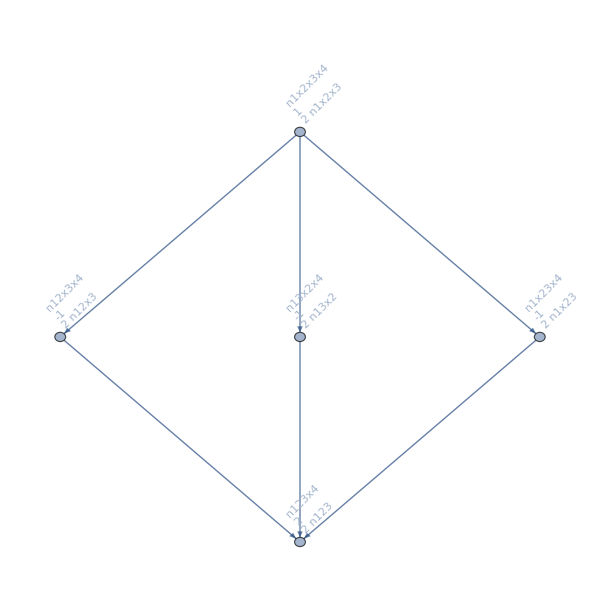

```mathematica
MobiusGraph4[333,allGraphs4]
```

```mathematica
allGraphs4[363,"graph"]
```

-Graphics-

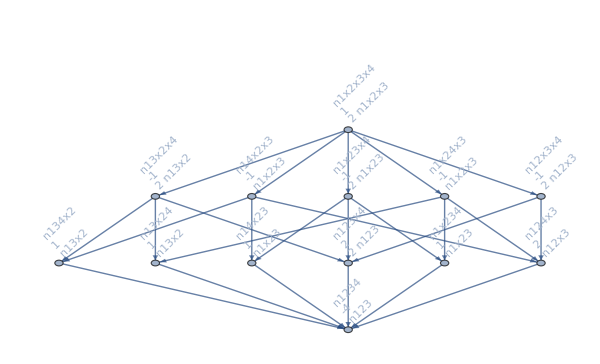

```mathematica
MobiusGraph4[363,allGraphs4]
```

```mathematica
Select[Keys[allGraphs5],IsomorphicGraphQ[VertexAdd[CompleteGraph[3],{4,5}],allGraphs5[#,"graph"]]&]
```

{26487,21951,20439,8757,7293,2917,333,273,109,13}

```mathematica
allGraphs5[26487,"graph"]
```

-Graphics-

```mathematica
Select[Keys[allGraphs5],IsomorphicGraphQ[EdgeAdd[CompleteGraph[3],4<->5],allGraphs5[#,"graph"]]&]
```

{26488,21954,20448,19696,8784,7374,6670,3160,2460,1062}

```mathematica
allGraphs5[26488,"graph"]
```

-Graphics-

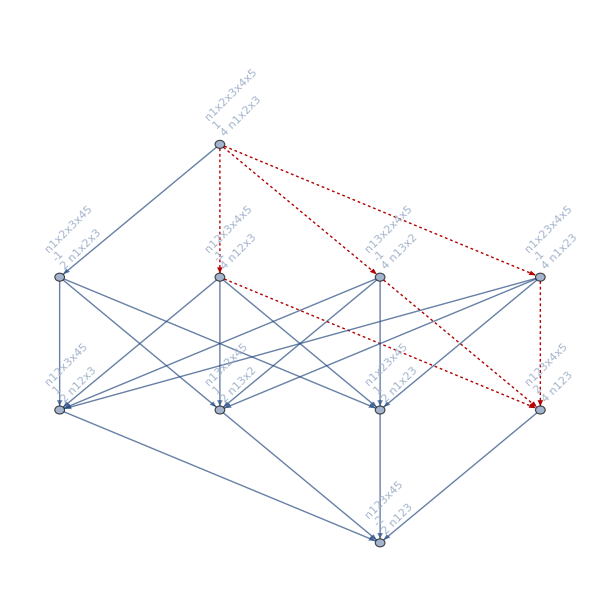

```mathematica
Graph[MobiusGraph4[26488,allGraphs5],GraphHighlight->EdgeList[MobiusGraph4[26487,allGraphs5]],GraphHighlightStyle->"Dotted"]
```

```mathematica
Select[Keys[allGraphs5],IsomorphicGraphQ[VertexAdd[CompleteGraph[2],{3,4,5}],allGraphs5[#,"graph"]]&]
```

{19683,6561,2187,729,243,81,27,9,3,1}

```mathematica
allGraphs5[19683,"graph"]
```

-Graphics-

```mathematica
MobiusGraph4[19683,allGraphs5]
```

-Graphics-

```mathematica
Select[Keys[allGraphs5],IsomorphicGraphQ[VertexAdd[EdgeAdd[CompleteGraph[2],4<->5],3],allGraphs5[#,"graph"]]&]
```

{19692,19686,19684,6642,6588,6562,2430,2214,2190,972,810,738,244,84,36}

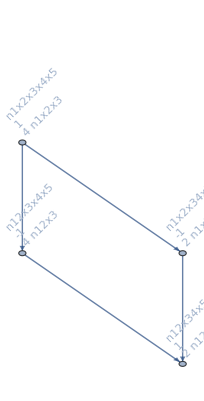

```mathematica
MobiusGraph4[19692,allGraphs5]
```

```mathematica
MobiusGraph4Bis[key_,allGraphs_]:=Block[{form=allGraphs[key,"colofour"], vars, blocks=Association[],c,edges,set, found=Association[],realyNullAtomKeys=Sort[Select[Keys[allGraphs],Length[ListofVars[allGraphs[#,"colofour"]]]==1&]]},
vars=ListofVars[form];
Table[blocks[k]={},{k,0,5}];
Table[
set=allGraphs[First[Select[realyNullAtomKeys,allGraphs[#,"colofour"]==v&]]];
found [v]=set;
set=set["vertexsets"];
c=Length[set];
blocks[c]=Append[blocks[c],{v,set}]
,{v,vars}];
edges={};
Table[
Table[
Table[
If[IsRefinement[from[[2]],to[[2]]],
AppendTo[edges,DirectedEdge[
to[[1]],
from [[1]]]]
],{to,blocks[k]}
],{from,blocks[k-1]}
]
,{k,1,5}];
Graph[vars,edges,VertexLabels->Table[n->Tooltip[Rotate[(TableForm[{n,Style[Coefficient[form,n],Bold,Blue], Style[DropMore[n,3],Red]},TableAlignments->Center]),Pi/4],found[n,"graph"]],{n,vars}],ImageSize->600,GraphLayout->"LayeredDigraphEmbedding"]
]
```

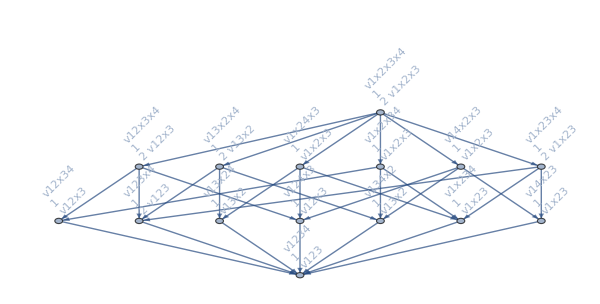

```mathematica
MobiusGraph4Bis[0,allGraphs4]
```

```mathematica
Select[Keys[allGraphs4],IsomorphicGraphQ[EdgeAdd[CompleteGraph[2],3<->4],allGraphs4[#,"graph"]]&]
```

{244,84,36}

```mathematica
With[
{k=84},
allGraphs4[k,"graph"]->
Labeled[
Graph[MobiusGraph4Bis[0,allGraphs4],GraphHighlight->
With[
{sub=MobiusGraph4Bis[k,allGraphs4]}
,
Join[EdgeList[sub],VertexList[sub]]
],
GraphHighlightStyle->"Dashed"],
{allGraphs4[k,"colofour"],CompleteBaseCoeff[ChromaticPolynomial[allGraphs4[k,"graph"],x]]},{Top,Bottom}]
]
```

-Graphics-→-Graphics-v12x34+v12x3x4+v14x23+v14x2x3+v1x23x4+v1x2x34+v1x2x3x4{0,0,2,4,1}

```mathematica
GraphElementData["GraphHighlightStyle"]
```

{Automatic,Dashed,Dotted,Thick,VertexConcaveDiamond,VertexDiamond,VertexTriangle,DehighlightFade,DehighlightGray,DehighlightHide}